BesselJ[0,5]

BesselJ[1,5]

0.485472

BesselJ[2,10]

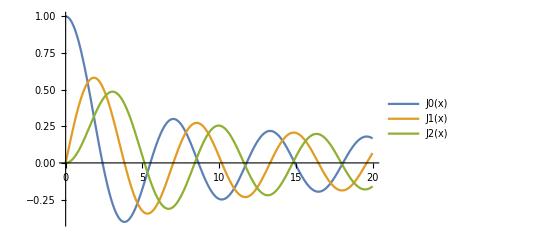

x^ν (2^-ν/Gamma[1+ν]-(2^(-2-ν) x^2)/((1+ν) Gamma[1+ν])+(2^(-5-ν) x^4)/((1+ν) (2+ν) Gamma[1+ν])+O[x]^6)

{{y[x]→(√2 ⅇ^((ⅈ x^2)/2) √(x^2) C[1] HypergeometricU[1/4 ⅈ (-2 ⅈ+ν^2),1,-ⅈ x^2])/x+(√2 ⅇ^((ⅈ x^2)/2) √(x^2) C[2] LaguerreL[-1/4 ⅈ (-2 ⅈ+ν^2),-ⅈ x^2])/x}}

```mathematica
(*1. Calcular valores de la función de Bessel Jn(x) en un punto dado*)BesselJ[0,5]   (*Bessel de orden 0 en x=5*)
BesselJ[1,5]   (*Bessel de orden 1 en x=5*)
BesselJ[2,3.14]

(*2. Definir una función y evaluarla numéricamente*)
f[x_]:=BesselJ[2,x]
f[10]   (*Evalúa J2(10)*)

(*3. Representar varias funciones de Bessel (de primer tipo) en un mismo gráfico*)
Plot[{BesselJ[0,x],BesselJ[1,x],BesselJ[2,x]},{x,0,20},PlotRange->All,PlotLegends->{"J0(x)","J1(x)","J2(x)"}]

(*4. Otras funciones de Bessel:-BesselY[ν,x]->Bessel de segundo tipo-BesselI[ν,x]->Bessel modificadas de primer tipo-BesselK[ν,x]->Bessel modificadas de segundo tipo*)

(*5. Expandir simbólicamente una Bessel alrededor de x=0*)
Series[BesselJ[ν,x],{x,0,5}]  (*Expansión en serie de potencia en x=0*)

(*6. Resolver ecuaciones diferenciales con Bessel (ejemplo simbólico)*)
DSolve[y''[x]+(1/x) y'[x]+(x^2-ν^2) y[x]==0,y[x],x]
```